```mathematica
SetDirectory["~/jennaproject/data"];
```

```mathematica
kvals=Import["kvals.txt","List"][[1;;425]];
plin=Import["plin.txt","List"][[1;;425]];
b1b2=Import["b1b2.txt","List"][[1;;425]];
b1br=Import["b1br.txt","List"][[1;;425]];
b2b2=Import["b2b2.txt","List"][[1;;425]];
b2br=Import["b2br.txt","List"][[1;;425]];
brbr=Import["brbr.txt","List"][[1;;425]];
tknw=Import["tk_nowiggle.dat","Table"];
```

```mathematica
Dimensions[tknw]
Dimensions[kvals]
```

{3000,2}

{425}

```mathematica
ns=0.966;
```

### Continuous (w/ Interpolations)

```mathematica
tknwfunc=Interpolation[tknw];
b1b2func=Interpolation[{kvals,b1b2}ᵀ];
b1brfunc=Interpolation[{kvals,b1br}ᵀ];
b2b2func=Interpolation[{kvals,b2b2}ᵀ];
b2brfunc=Interpolation[{kvals,b2br}ᵀ];
brbrfunc=Interpolation[{kvals,brbr}ᵀ];
plinfunc=Interpolation[{kvals,plin}ᵀ];
```

```mathematica
psnwfunc[k_]:=4.0*10^6*k^ns*tknwfunc[k]^2;
```

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

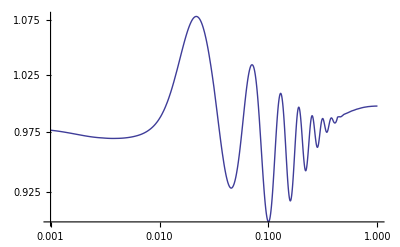

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

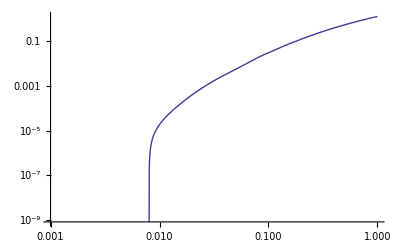

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

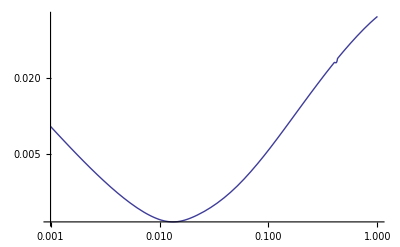

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

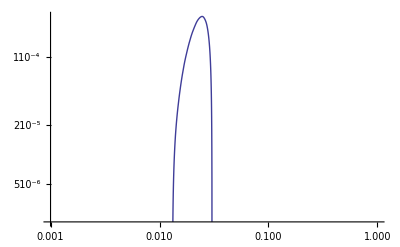

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

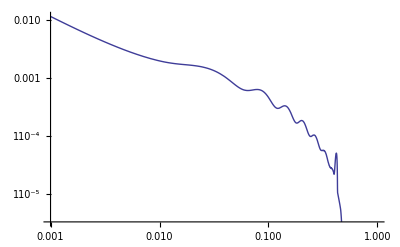

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

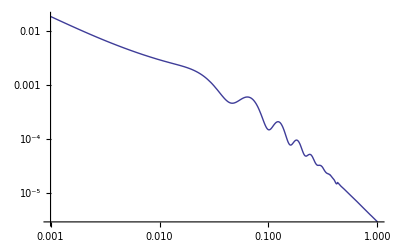

```mathematica
LogLogPlot[plinfunc[k]/psnwfunc[k],{k,0.001,1}]
LogLogPlot[b1b2func[k]/psnwfunc[k],{k,0.001,1}]
LogLogPlot[b2b2func[k]/psnwfunc[k],{k,0.001,1}]
LogLogPlot[b1brfunc[k]/psnwfunc[k],{k,0.001,1}]
LogLogPlot[b2brfunc[k]/psnwfunc[k],{k,0.001,1}]
LogLogPlot[brbrfunc[k]/psnwfunc[k],{k,0.001,1}]
```

### Discrete (w/ data)

```mathematica
psnw=psnwfunc[#]&/@kvals;
```

```mathematica
mark1=Graphics[{Blue,Disk[]}];
mark2=Graphics[{Red,Disk[]}];
mark3=Graphics[{Orange,Disk[]}];
```

```mathematica
ListLogLogPlot[{{kvals,psnw}ᵀ,{kvals,plin}ᵀ},PlotMarkers->{{mark1,.02},{mark2,.015}}];
```

```mathematica
ListPlot[{kvals,plin-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
```

```mathematica
ListPlot[{kvals,b1b2-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b1br-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b2b2-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b2br-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,brbr-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
```